```mathematica
(*Observed*)
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Codes\\6\\data2019.xlsx";
SystemOpen@csvPath
Data = Import[csvPath];
AllDate=Data[[1]][[2;;-1]];
For[i=1,i<=Length[AllDate],i++,AllDate[[i,1]]=DateObject[AllDate[[i,1]]][[1;;1,1;;3]]][[1]];
Count2=Count1;
For[i=2,i<=Length[AllDate],i++,
Count2[[i,2]]=Count2[[i-1,2]]+Count2[[i,2]]
];
```

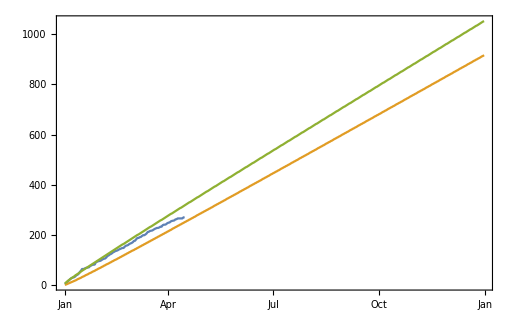

```mathematica
(*Predicted full year*)
Countl={};
Countu={};
DayTemp = DateObject[{2019,1,1,0,0,0.},"Instant","Gregorian",8.];
For[m=1,m≤365,m++,l=Ceiling[3943/1461*m-1.96*Sqrt[a*m^2*(1/m+1/1461)]];
u=Floor[3943/1461*m+1.96*Sqrt[a*m^2*(1/m+1/1461)]];
LowTemp = {DayPlus[DayTemp,m-1],l};
UpTemp={DayPlus[DayTemp,m-1],u};
Countl=Insert[Countl,LowTemp,-1];
Countu=Insert[Countu,UpTemp,-1];
];
(*Plot*)
DateListPlot[{Count2,Countl,Countu}]
```

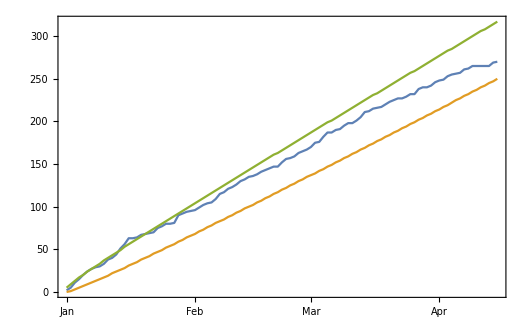

```mathematica
(*Predicted till Apr. 15th*)
Countl={};
Countu={};
DayTemp = DateObject[{2019,1,1,0,0,0.},"Instant","Gregorian",8.];
For[m=1,m≤31+28+31+15,m++,l=Ceiling[3943/1461*m-1.96*Sqrt[a*m^2*(1/m+1/1461)]];
u=Floor[3943/1461*m+1.96*Sqrt[a*m^2*(1/m+1/1461)]];
LowTemp = {DayPlus[DayTemp,m-1],l};
UpTemp={DayPlus[DayTemp,m-1],u};
Countl=Insert[Countl,LowTemp,-1];
Countu=Insert[Countu,UpTemp,-1];
];
(*Plot*)
DateListPlot[{Count2,Countl,Countu}]
```